```mathematica
Clear[ϕ,W,h,x,hSummary];
ϕ[x_]:=Min[x,0]
W[0][x_]=ϕ[x];
(*W[1][x_]=Integrate[ϕ[x-2u+1],{u,0,1}]//FullSimplify
W[2][x_]=Integrate[ϕ[x-2u1+1-2u2+1],{u1,0,1},{u2,0,1}]//FullSimplify
W[3][x_]=Integrate[ϕ[x-2u1+1-2u2+1-2u3+1],{u1,0,1},{u2,0,1},{u3,0,1}]//FullSimplify
W[4][x_]=Integrate[ϕ[x-2u1+1-2u2+1-2u3+1-2u4+1],{u1,0,1},{u2,0,1},{u3,0,1},{u4,0,1}]//FullSimplify*)


W[1][x_]:=Piecewise[{{x, x≤-1}, {-1/4 (-1+x)^2, -1<x<1}, {0, True}}]
W[2][x_]:=Piecewise[{{1/24 (-2+x)^3, 0<x<2}, {x, x≤-2}, {1/24 (-8-x (-12+x (6+x))), -2<x≤0}, {0, True}}]
W[3][x_]:=Piecewise[{{-1/192 (-3+x)^4, 1≤x<3}, {x, x≤-3}, {1/192 (-81-x (-84+x (54+x (12+x)))), -3<x≤-1}, {1/96 (-39+x (48-18 x+x^3)), -1<x<1}, {0, True}}]
W[4][x_]:=Piecewise[{{(-896+x (960-320 x+20 x^3-3 x^4))/1920, 0≤x<2}, {(-4+x)^5/1920, 2≤x<4}, {x, x≤-4}, {(-1024-x (-640+x (640+x (160+x (20+x)))))/1920, -4<x≤-2}, {(-896+x (960-320 x+20 x^3+3 x^4))/1920, -2<x<0}, {0, True}}]
W[5][x_]:=Piecewise[{{(-5995-3 x (-1920+575 x-25 x^3+x^5))/11520, -1≤x≤1}, {-(-5+x)^6/23040, 3≤x<5}, {x, x≤-5}, {(-15625-x (-4290+x (9375+x (2500+x (375+x (30+x))))))/23040, -5<x≤-3}, {(-2995+x (2865+x (-825+x (-50+x (75+(-15+x) x)))))/5760, 1<x<3}, {(-2995+x (2895+x (-825+x (50+x (75+x (15+x))))))/5760, -3<x<-1}, {0, True}}]

h[n_][x_][u_]:=Assuming[
0≤u≤1,
FullSimplify[
u^(-2) Integrate[2s (W[n-1])'[x+1-2s],{s,0,u},Assumptions->{x∈Reals,u∈Reals,0<=u<=1}]
]
]
h[1][x_][u_]:=Piecewise[{{1, u>0&&x≤-1}, {-(-4 u^2+(1+x)^2)/(4 u^2), x>-1&&2 u>1+x}, {0, True}}]
h[2][x_][u_]:=Piecewise[{{u^2, u>0&&2+x≤0}, {1/6 u^2 (4 u-3 x), 2 u<2+x&&u>0&&x≤0}, {-1/24 (-4+x) (2+x)^2, 2 u==2+x&&x>-2}, {1/24 (24 u^2-(2+x)^3), 2 u>2+x&&x>-2}, {1/24 (-2 u+x)^2 (4 u+x), x<2 u&&x>0}, {0, True}}]/u^2
h[3][x_][u_]:=Piecewise[{{u^2, u>0&&3+x≤0}, {1/192 (1+2 u-x)^3 (-1+6 u+x), x<1+2 u&&x>1}, {1/192 (1+x)^2 (17+(-6+x) x), 2 u==1+x&&x>-1}, {1/24 u^2 (6 u^2-8 u (-1+x)+3 (-1+x)^2), 2 u<1+x&&u>0&&x≤1}, {-1/24 u^2 (6 u^2-8 u (3+x)+3 (1+x (6+x))), u>0&&x≤-1&&2 u<3+x}, {1/192 (192 u^2-(3+x)^4), 2 u>3+x&&x>-3}, {-1/192 (3+x)^2 (-39+x (6+x)), 2 u==3+x&&-3<x≤-1}, {1/96 (-24 u^4+(1+x)^4+32 u^3 (3+x)-12 u^2 (1+x (6+x))), 1+x<2 u&&x>-1}, {0, True}}]/u^2
h[4][x_][u_]:=1/u^2 Piecewise[{{u^2, u>0&&4+x≤0}, {((-2-2 u+x)^4 (-2+8 u+x))/1920, x<2+2 u&&x>2}, {1/240 u^2 (16 u^3-30 u^2 (-2+x)+20 u (-2+x)^2-5 (-2+x)^3), 2 u<x&&u>0&&x≤2}, {-(x^2 (-80+x (40+(-10+x) x)))/1920, 2 u==x&&x>0}, {1/240 u^2 (16 u^3-30 u^2 (4+x)+20 u (4+x)^2-5 (16+x (48+x (12+x)))), u>0&&x≤-2&&2 u<4+x}, {1/120 u^2 (-16 u^3+30 u^2 (1+x)-20 u (-2+x (2+x))+5 (4+x (-6+x (3+x)))), u>0&&x≤0&&2 u<2+x}, {(-256 u^5-3 x^5+480 u^4 (1+x)-320 u^3 (-2+x (2+x))+80 u^2 (4+x (-6+x (3+x))))/1920, x<2 u&&x>0}, {u^2-(4+x)^5/1920, 2 u>4+x&&x>-4}, {-((4+x)^2 (-416+x (48+x (12+x))))/1920, 2 u==4+x&&-4<x≤-2}, {1/960 (2+x)^2 (148+x (-28+x+x^2)), 2 u==2+x&&-2<x≤0}, {(128 u^5+3 (2+x)^5-240 u^4 (4+x)+160 u^3 (4+x)^2-40 u^2 (16+x (48+x (12+x))))/1920, 2+x<2 u&&x>-2}, {0, True}}]
h[5][x_][u_]:=1/u^2 Piecewise[{{u^2, u>0&&5+x≤0}, {((3+2 u-x)^5 (-3+10 u+x))/23040, x<3+2 u&&x>3}, {((-1+x)^2 (473+x (-320+x (102+(-16+x) x))))/23040, 1+2 u==x&&x>1}, {(u^2 (80 u^4-192 u^3 (-3+x)+180 u^2 (-3+x)^2-80 u (-3+x)^3+15 (-3+x)^4))/5760, 1+2 u<x&&u>0&&x≤3}, {1/5760 u^2 (-240 u^4+192 u^3 (-1+3 x)+180 u^2 (5+(2-3 x) x)-15 (-7+x (2+x)) (11+x (-10+3 x))+80 u (23+3 x (-5+(-1+x) x))), u>0&&2 u<1+x&&x≤1}, {1/5760 u^2 (-80 u^4+192 u^3 (5+x)-180 u^2 (5+x)^2+80 u (5+x)^3-15 (241+x (10+x) (50+x (10+x)))), u>0&&x≤-3&&2 u<5+x}, {1/5760 u^2 (240 u^4-192 u^3 (7+3 x)+180 u^2 (1+x) (11+3 x)-80 u (-17+3 x (11+x (7+x)))+15 (83+x (-68+x (66+x (28+3 x))))), u>0&&x≤-1&&2 u<3+x}, {1/11520(480 u^6-3 (1+x)^6-384 u^5 (7+3 x)+360 u^4 (1+x) (11+3 x)-160 u^3 (-17+3 x (11+x (7+x)))+30 u^2 (83+x (-68+x (66+x (28+3 x))))), 1+x<2 u&&x>-1}, {-((1+x)^2 (-2261+x (580+3 x (-18+(-4+x) x))))/23040, 2 u==1+x&&-1<x≤1}, {(23040 u^2-(5+x)^6)/23040, 2 u>5+x&&x>-5}, {-((5+x)^2 (-5135+x (10+x) (50+x (10+x))))/23040, 2 u==5+x&&-5<x≤-3}, {1/5760(-240 u^6+(-1+x)^6+192 u^5 (-1+3 x)+180 u^4 (5+(2-3 x) x)-15 u^2 (-7+x (2+x)) (11+x (-10+3 x))+80 u^3 (23+3 x (-5+(-1+x) x))), x<1+2 u&&x>1}, {1/5760(-80 u^6+(3+x)^6+192 u^5 (5+x)-180 u^4 (5+x)^2+80 u^3 (5+x)^3-15 u^2 (241+x (10+x) (50+x (10+x)))), 3+x<2 u&&x>-3}, {((3+x)^2 (4419+x (-520+3 x (-2+x (8+x)))))/23040, 2 u==3+x&&-3<x≤-1}, {0, True}}]
hSummary[n_,x_]:=
Module[{f,t,p,cdf,g},
f[u_] = Assuming[0≤u≤1,Simplify[h[n][x][u]]];
t= Framed[f[u]];
p = Plot[f[u],{u,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->{Red,Thick}];
ppl=ParametricPlot[{f[u],u},{u,0,1},PlotStyle->Thick];
g=Show[p,ppl];
GraphicsGrid[{{t},{g}}]
]
```

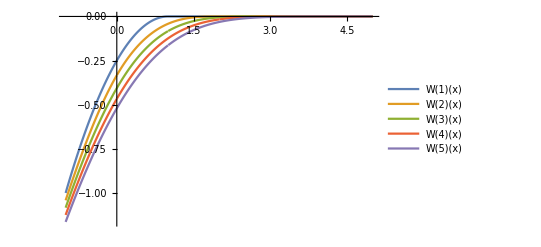

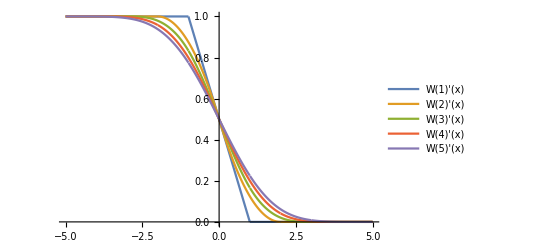

```mathematica
Plot[{W[1][x],W[2][x],W[3][x],W[4][x],W[5][x]},{x,-1,5}, PlotLegends->"Expressions",PlotPoints->1000]
Plot[{W[1]'[x],W[2]'[x],W[3]'[x],W[4]'[x],W[5]'[x]},{x,-5,5}, PlotLegends->"Expressions",PlotPoints->1000]
```

```mathematica
Manipulate[
hSummary[n,x],
{n,1,5,1},
{x,-5,5,0.01}
]
```

V[n_][p_] := NMinimize[p x - W[n][x], x][[1]]
Plot[{V[1][p], V[2][p], V[3][p], V[4][p], V[5][p]}, {p, 0, 1.1}, PlotLegends -> "Expressions", PlotPoints -> 10]

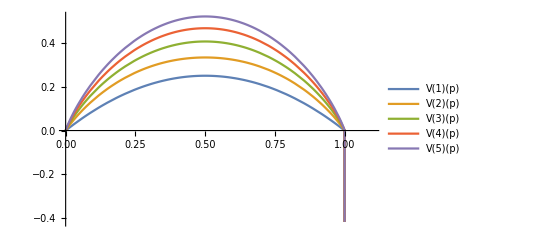

```mathematica
tauSummary[p_]:=
Module[{f,x,xf,g,t,pl},
x=1-2p;
f[u_] = Assuming[0≤u≤1,Simplify[h[1][x][u]]];
xf=Framed[x];
t= Framed[f[u]];
pl = Plot[f[u],{u,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->{Red,Thick}];
ppl=ParametricPlot[{f[u],u},{u,0,1},PlotStyle->Thick];
g=Show[{pl,ppl}];
GraphicsGrid[{{t},{g}}]
]
```

```mathematica
Manipulate[
tauSummary[p],
{p,0,1/2,0.01}
]
```

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
Manipulate[
Plot[
{
D[W[0][y],y]/.y->x-2s+1//Simplify,
D[W[1][y],y]/.y->x-2s+1//Simplify,
D[W[2][y],y]/.y->x-2s+1//Simplify,
D[W[3][y],y]/.y->x-2s+1//Simplify
},
{s,0,1}
],
{x,-1,3}
]
```

```mathematica
ht[p_,u_,β_]:=Piecewise[{
{0,u<1-p},
{1-(β-p)^2/(u-(1-β))^2,u>1-p}
}]
```

```mathematica
Manipulate[
Show[
Plot[ht[p,u,β],{u,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->Red],
ParametricPlot[{ht[p,u,β],u},{u,0,1},PlotStyle->Blue]
],
{p,0,1/2,0.01},
{β,1/2,1,0.01}
]
```